```mathematica
Solve[x+x*a-x*a(x/c)== r,x]
```

{{x→(c+a c-√c √(c+2 a c+a^2 c-4 a r))/(2 a)},{x→(c+a c+√c √(c+2 a c+a^2 c-4 a r))/(2 a)}}

```mathematica
Export[x->1/2 (c-√(c^2+4 b r-4 c r-4 b xa+4 c xa+4 b z-4 c z))},{x->1/2 (c+√(c^2+4 b r-4 c r-4 b xa+4 c xa+4 b z-4 c z)]
```

```mathematica
TeXForm[x->1/2 (-a b+c+a c+√((-a b+c+a c)^2+4 (b r-c r+b z-c z)))]
```

x\to \frac{1}{2} \left(\sqrt{(-a b+a c+c)^2+4 (b r+b z-c r-c
   z)}-a b+a c+c\right)

```mathematica
Graph[1/2 (-a b+c+a c-√((-a b+c+a c)^2+4 (b r-c r+b z-c z))),{c,0,100}]
```

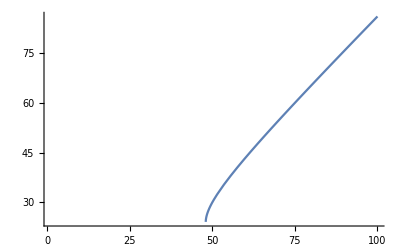

```mathematica
Plot[1/2 (c+√((c)^2+4 (-c 10-c 2))),{c,1,100}]
```

```mathematica
(p(g(x-1)-p+r))/(xg-p+r)
```

```mathematica
f[p_]:=(p(g(x-1)-p+r))/(xg-p+r)
Simplify[f'[p]]
```

(p^2-2 p (r+xg)+(r+g (-1+x)) (r+xg))/(-p+r+xg)^2

```mathematica
TeXForm[(p^2-2 p (r+xg)+(r+g (-1+x)) (r+xg))/(-p+r+xg)^2]
```

\frac{(r+\text{xg}) (g (x-1)+r)+p^2-2 p
   (r+\text{xg})}{(-p+r+\text{xg})^2}

```mathematica
Solve[(p^2-2 p (r+xg)+(r+g (-1+x)) (r+xg))/(-p+r+xg)^2== 0,p]
```

{{p→r+xg-√(g r-g r x+g xg+r xg-g x xg+xg^2)},{p→r+xg+√(g r-g r x+g xg+r xg-g x xg+xg^2)}}

```mathematica
TeXForm[r+xg-√(g r-g r x+g xg+r xg-g x xg+xg^2)]
```

-\sqrt{-g r x+g r-g x \text{xg}+g \text{xg}+r
   \text{xg}+\text{xg}^2}+r+\text{xg}

```mathematica
Simplify[r+xg-√(g r-g r x+g xg+r xg-g x xg+xg^2)]
```

r+xg-√((r+xg) (g-g x+xg))

```mathematica
TeXForm[r+xg-√((r+xg) (g-g x+xg))]
```

-\sqrt{(r+\text{xg}) (g (-x)+g+\text{xg})}+r+\text{xg}

```mathematica
Simplify[(r+xg-√(g r-g r x+g xg+r xg-g x xg+xg^2))(1-1/(x-((r+xg-√(g r-g r x+g xg+r xg-g x xg+xg^2))-r)/g))]
```

```mathematica
-((-r-x*g+√((r+x*g) (g-g*x+x*g))) (g (-1+x)-x*g+√((r+x*g) (g-g x+x*g))))/(g* x-x*g+√((r+x*g) (g-g*x+x*g)))
```

-((-r-g x+√(g (r+g x))) (g (-1+x)-g x+√(g (r+g x))))/(√(g (r+g x)))

```mathematica
{xg,-2,2}]
```